```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
f[x__]:=Log[PDF[MultinormalDistribution[{5,5},{{1.5,0.25},{0.25,1.5}}],{x}]][[1]]
fDerivative[f_,z_]:=Module[{x,v},v=Array[x,Length[z]];
D[f@@v,{v}]/.Thread[v->z]]
fLeapFrogStep[θ_,m_,ϵ_,logP_]:=Module[{grad,x,θ1,m1,grad1},grad=fDerivative[logP,θ];m1=m+0.5 ϵ grad; θ1=θ+ϵ m1;grad1=fDerivative[logP,θ1];m1=m1+0.5 ϵ grad1;{θ1,m1}]
fBuildTree[θ_,m_,u_,v_,j_,ϵ_,logP_,Δ_]:=Module[{Cprimed,Cprimedprimed,sprimed,sprimedprimed,res,thetaMinus,thetaPlus,mMinus,mPlus,temp1,temp2},If[j==0,res=fLeapFrogStep[θ,m,v ϵ,logP];Cprimed=If[Log[u]≤(logP[res[[1]]]-0.5 m.m),res,{}];sprimed=If[Log[u]<(Δ+logP[res[[1]]]-0.5 m.m),1,0]; {res[[1]],res[[2]],res[[1]],res[[2]],Cprimed,sprimed},{thetaMinus,mMinus,thetaPlus,mPlus,Cprimed,sprimed}=fBuildTree[θ,m,u,v,j-1,ϵ,logP,Δ];If[v==-1,{thetaMinus,mMinus,temp1,temp2,Cprimedprimed,sprimedprimed}=fBuildTree[thetaMinus,mMinus,u,v,j-1,ϵ,logP,Δ],
{temp1,temp2,thetaPlus,mPlus,Cprimedprimed,sprimedprimed}=fBuildTree[thetaPlus,mMinus,u,v,j-1,ϵ,logP,Δ]];sprimed=sprimed sprimedprimed If[(thetaPlus-thetaMinus).mMinus ≥ 0,1,0]If[(thetaPlus-thetaMinus).mPlus ≥ 0,1,0];Cprimed = Union[{Cprimed},{Cprimedprimed}]; {thetaMinus,mMinus,thetaPlus,mPlus,Cprimed,sprimed}]]
fNUTSstep[θ_,ϵ_,logP_,Δ_]:=Module[{thetaMinus=θ,thetaPlus=θ,mMinus,mPlus,j=0,C,s=1,m,temp1,temp2,Cprimed,sprimed,u,v},m=RandomVariate[MultinormalDistribution[ConstantArray[0,Length@θ],IdentityMatrix[Length@θ]],{1}][[1]];u=RandomVariate[UniformDistribution[{0,Exp[logP[θ]-0.5 m.m]}],1][[1]];
mMinus=m;mPlus=m;C={θ,m};While[s==1,v=RandomChoice[{-1,1}];If[v==-1,{thetaMinus,mMinus,temp1,temp2,Cprimed,sprimed}=fBuildTree[thetaMinus,mMinus,u,v,j,ϵ,logP,Δ],{temp1,temp2,thetaPlus,mPlus,Cprimed,sprimed}=fBuildTree[thetaPlus,mPlus,u,v,j,ϵ,logP,Δ]];
If[sprimed==1,C=Union[{C},{Cprimed}]];
s=sprimed If[(thetaPlus-thetaMinus).mMinus ≥ 0,1,0]If[(thetaPlus-thetaMinus).mPlus ≥ 0,1,0];j = j + 1];C]
fNUTSstepExtract[c_]:=Module[{dep=Depth@c},RandomChoice@DeleteCases[Flatten[c,dep-4],{}]]
fNUTSstepComplete[θ_,ϵ_,logP_,Δ_]:=Module[{c=fNUTSstep[θ,ϵ,logP,Δ]},fNUTSstepExtract[c]]
fNUTS[M_Integer,θ0_,ϵ_,logP_,Δ_]:=NestList[fNUTSstepComplete[#[[1]],ϵ,logP,Δ]&,{θ0,{}},M]
```

```mathematica
samples=fNUTS[50,{0,0},0.1,f,1000];
```

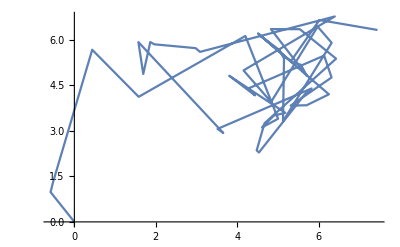

```mathematica
ListLinePlot[samples[[All,1]]]
```

## Visualising tree

```mathematica
fNUTSstepSingle[θ_,ϵ_,logP_,Δ_]:=Module[{thetaMinus=θ,thetaPlus=θ,mMinus,mPlus,j=0,C,s=1,m,temp1,temp2,Cprimed,sprimed,u,v},m=RandomVariate[MultinormalDistribution[ConstantArray[0,Length@θ],IdentityMatrix[Length@θ]],{1}][[1]];u=RandomVariate[UniformDistribution[{0,Exp[logP[θ]-0.5 m.m]}],1][[1]];
mMinus=m;mPlus=m;C={θ,m};v=RandomChoice[{-1,1}];If[v==-1,{thetaMinus,mMinus,temp1,temp2,Cprimed,sprimed}=fBuildTree[thetaMinus,mMinus,u,v,j,ϵ,logP,Δ],{temp1,temp2,thetaPlus,mPlus,Cprimed,sprimed}=fBuildTree[thetaPlus,mPlus,u,v,j,ϵ,logP,Δ]];
If[sprimed==1,C=Union[{C},{Cprimed}]];
s=sprimed If[(thetaPlus-thetaMinus).mMinus ≥ 0,1,0]If[(thetaPlus-thetaMinus).mPlus ≥ 0,1,0];j = j + 1;C]
fNUTSstepSingleString[thetaMinus_,mMinus_,thetaPlus_,mPlus_,C_,j_,s_,u_,ϵ_,logP_,Δ_]:=Module[{thetaMinus1=thetaMinus,mMinus1=mMinus,thetaPlus1=thetaPlus,mPlus1=mPlus,s1=s,temp1,temp2,Cprimed,sprimed,v,C1,j1,dep},
v=RandomChoice[{-1,1}];If[v==-1,{thetaMinus1,mMinus1,temp1,temp2,Cprimed,sprimed}=fBuildTree[thetaMinus1,mMinus1,u,v,j,ϵ,logP,Δ],{temp1,temp2,thetaPlus1,mPlus1,Cprimed,sprimed}=fBuildTree[thetaPlus1,mPlus,u,v,j,ϵ,logP,Δ]];
dep=Depth@Cprimed-4;
If[sprimed==1,C1=Join[{C},{Cprimed}]];
s1=sprimed If[(thetaPlus1-thetaMinus1).mMinus1 ≥ 0,1,0]If[(thetaPlus1-thetaMinus1).mPlus1 ≥ 0,1,0];j1 = j + 1;{thetaMinus1, mMinus1, thetaPlus1, mPlus1,C1,j1,s1,u,ϵ,logP,Δ}]
fBuildTree[θ_,m_,u_,v_,j_,ϵ_,logP_,Δ_]:=Module[{Cprimed,Cprimedprimed,sprimed,sprimedprimed,res,thetaMinus,thetaPlus,mMinus,mPlus,temp1,temp2},If[j==0,res=fLeapFrogStep[θ,m,v ϵ,logP];Cprimed=If[Log[u]≤(logP[res[[1]]]-0.5 m.m),res,{res[[1]],res[[2]],{}}];sprimed=If[Log[u]<(Δ+logP[res[[1]]]-0.5 m.m),1,0]; {res[[1]],res[[2]],res[[1]],res[[2]],Cprimed,sprimed},{thetaMinus,mMinus,thetaPlus,mPlus,Cprimed,sprimed}=fBuildTree[θ,m,u,v,j-1,ϵ,logP,Δ];If[v==-1,{thetaMinus,mMinus,temp1,temp2,Cprimedprimed,sprimedprimed}=fBuildTree[thetaMinus,mMinus,u,v,j-1,ϵ,logP,Δ],
{temp1,temp2,thetaPlus,mPlus,Cprimedprimed,sprimedprimed}=fBuildTree[thetaPlus,mMinus,u,v,j-1,ϵ,logP,Δ]];sprimed=sprimed sprimedprimed If[(thetaPlus-thetaMinus).mMinus ≥ 0,1,0]If[(thetaPlus-thetaMinus).mPlus ≥ 0,1,0];Cprimed = DeleteCases[Union[{Cprimed},{Cprimedprimed}],{}]; {thetaMinus,mMinus,thetaPlus,mPlus,Cprimed,sprimed}]]
```

```mathematica
fNUTSstring[theta0_,m0_,u_,ϵ_,logP_,Δ_]:=NestWhileList[fNUTSstepSingleString@@#&,{theta0,m0,theta0,m0,{theta0,m0},0,1,u,ϵ,logP,Δ},#[[7]]==1 &]
```

```mathematica
fUnravel[lTree__]:=Module[{len=(Length@lTree)-1,lDeps,lAll},lDeps=Table[Depth@lTree[[i]][[5]],{i,1,len,1}];lAll=Table[Flatten[lTree[[i]][[5]],If[lDeps[[i]]-4>0,lDeps[[i]]-4,0]],{i,1,len,1}];Table[If[i==1,{lAll[[i]]},lAll[[i]]],{i,1,len,1}]]
```

```mathematica
f[x__]:=Log[PDF[MultinormalDistribution[{5,5},{{1.5,0.},{0.,1.5}}],{x}]][[1]]
```

```mathematica
test=fNUTSstring[{4.6,5.4},{0.1,-0.2},1,0.5,f,1000];
```

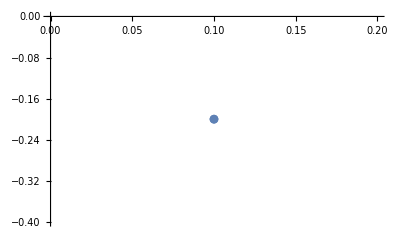
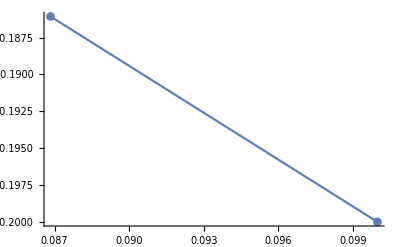
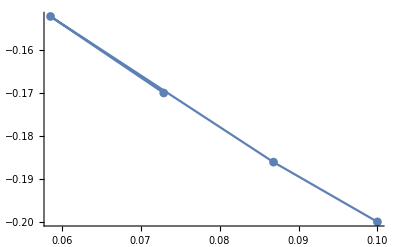
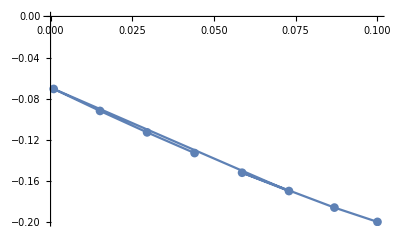

```mathematica
lAnimations=Table[ListPlot[fUnravel[test][[i]][[All,2]],Joined->True,PlotMarkers->Automatic,PlotRange->Automatic],{i,1,Length@test-1,1}]
```

```mathematica
ListAnimate[lAnimations]
```